# Late time approaches to the Hubble tension deforming H(z), worsen the growth tension - G. Alestas and L. Perivolaropoulos - Figure 2

## Section III - Growth of Perturbations and the Growth Tension in Hubble Deformation Models

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol];
```

```mathematica
h0pl=0.674; 
obh2=0.02236;
om0pl=0.315; 
orh2=(1+3.046*7/8*(4/11)^(4/3))2.473*10^(-5);
omh2=om0pl h0pl^2;
h0r=0.7403;
zrec=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(omh2)^(0.560/(1+21.1(obh2)^1.81)));
```

```mathematica
(* Define CPL model *)
```

```mathematica
wcpl[z_,w0_,w1_]:=w0+w1 z/(z+1)
decpl=Exp[3 Integrate[(1+wcpl[zp,w0,w1])/(1+zp),{zp,0,z},Assumptions->z>0]];
Hcpl[z_,h_,w0_,w1_]:=√(omh2 (1+z)^3+orh2  (1+z)^4+(h^2 -omh2-orh2 )ⅇ^(3 (-(w1 z)/(1+z)+(1+w0+w1) Log[1+z])))
comdz[zmax_?NumberQ,hh_,w0_,w1_]:=NIntegrate[1/Hcpl[z,hh,w0,w1],{z,0,zmax}];
```

```mathematica
(* For given w0 what is the w1 that addresses the Hubble tension (consistent with CMB and Hcpl[0]=h0r) *)
```

```mathematica
w1ht[w0_]:=Part[FindRoot[comdz[zrec,h0r,w0,w1]==comdz[zrec,h0pl,-1,0],{w1,0}],1,2]//Chop
```

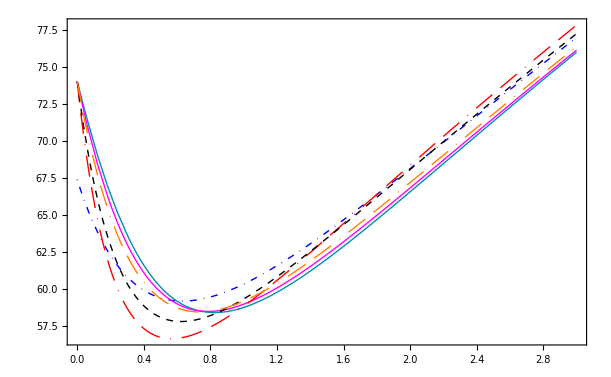

```mathematica
d1=.025;
d2=.001;
plt1=Plot[{100Hcpl[z,h0pl,-1,0]/(1+z),100Hcpl[z,h0r,-1,-0.93]/(1+z),100Hcpl[z,h0r,-1.1,-0.497]/(1+z),100Hcpl[z,h0r,-1.73,1.72]/(1+z),100Hcpl[z,h0r,-1.5,1.05]/(1+z),100Hcpl[z,h0r,-1.22,0]/(1+z)},{z,0,3},Frame->True,PlotStyle->{{Blue,Thick,DotDashed},{RGBColor[0.,0.56,0.69],Thick},{Magenta,Thick},{Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Red,Thick},{Dashed,Black,Thick},{Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Orange,Thick}}]
```

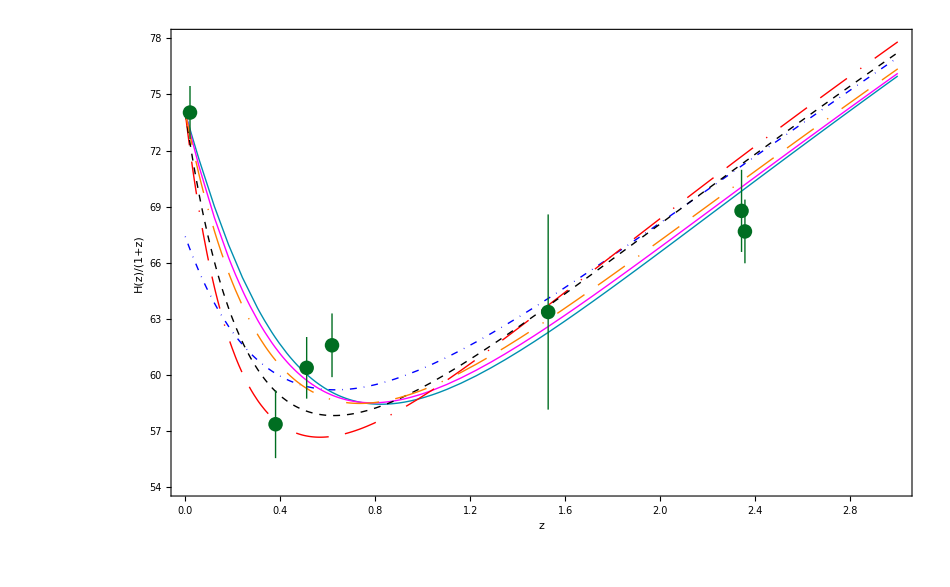

```mathematica
plt2=Show[plt1,PlotRange->{54,78},Frame->True,FrameLabel->{"z","H(z)/(1+z)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->950,Axes->False,Prolog->Inset[Framed[Column[{LineLegend[{Directive[DotDashed,Blue],Thick},{"ΛCDM"}],LineLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],RGBColor[0.,0.56,0.69]],Thick},{"w_0 = -1, w_1= -0.93"}],LineLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Magenta],Thick},{"w_0 = -1.1, w_1= -0.497"}],LineLegend[{Directive[DotDashed,Black],Thick},{"w_0 = -1.5, w_1 = 1.05"}],LineLegend[{Directive[Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Red],Thick},{"w_0 = -1.73, w_1 = 1.72"}],LineLegend[{{Directive[Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Orange]},Thick},{"wCDM (w = -1.22)"}]}],RoundingRadius->5],Scaled[{0.84,0.24}],BaseStyle -> {FontFamily->"Times",18}]];
listerror={{0.38024299678308426,Around[57.3592577166101,60.76582093388042-58.95265018920428]},{0.51123261934935,Around[60.37642346310295,-60.37642346310295+62.02476050371762]},{0.6179757357698,Around[61.581304667629674,-61.581304667629674+63.284763516806834]},{1.5280837638801503,Around[63.36115419040952,63.36115419040952-58.14142022846306]},{2.3565459363174734,Around[67.67146693134588,-67.67146693134588+69.37474853998104]},{2.3422825036998964,Around[68.77089001338166,68.77089001338166-66.5732845331041]},{0.02,Around[74.03,1.42]}};
plt3=ListPlot[listerror,PlotStyle->RGBColor[0.,0.43,0.13]];
pltHZ=Show[plt2,plt3]
```

```mathematica
Export[NotebookDirectory[]<>"Fig2.pdf",pltHZ,ImageResolution->1000];
```